# DG Package

## 1) Instance Creation and Plot Routines

Instance Creation: DG 
DGProblem, DGSaveProblem, 
DGAllEdges, DGEdgeWeight, DGEdgeDistanceBounds, DGGraphGetIJD

-Graphics-

## Source Code

```mathematica
ClearAll[
DGAllEdges,
DGEdgeWeight,
DGEdgeDistanceBounds,
DGProblem,
DGPrintData,
DGPrintX,
DGPrintDistanceMatrix,
DGSaveProblem,
DGGraphGetIJD
  ];

DGAllEdges[n_] := Module[{i, j, k = 0, pij},
   pij = Table[0, {i, (n (n - 1))/2}];
   For[i = 1, i <= n, i++,
    For[j = (i + 1), j <= n, j++,
      k++;
      pij[[k]] = i <-> j;
      ];
    ];
   Return[pij]
   ];

DGEdgeWeight[G_, E_] :=
  (* Gets edge weight. 'E' can be a single edge or a list of edges; *)
  Module[
{i, eij,wij, D = {}},
If[Not[FailureQ[PropertyValue[{G, E[[1]]}, EdgeWeight]]],
(* E is a list of edges *)
For[i = 1, i <= Length[E], i++,
eij = E[[i]];
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[wij=PropertyValue[{G, eij}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]];
AppendTo[D, wij]],
(* E is a single edge *)
eij = E;
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[D = PropertyValue[{G, E}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]]
];
Return[D]
];

DGEdgeDistanceBounds[G_, E_] := Module[
   {eij = E, Lij, Uij, Vij},
   If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
   Vij = PropertyValue[{G, eij}, "DistanceBounds"];
   Return[Vij]
   ];

DGProblem[x_,eij_: {},dijEps_: {}] :=
  (* Creates a problem P such that P["G"] is the problem graph and P["X"] is a problem solution; *)
  Module[{i,j,d,dij,k,numberOfAtoms,G,E,DijEps},
   (* set default values *)
   If[Length[eij]>0,E=eij,E=DGAllEdges[Length[x]]];
   If[Length[dijEps]>0,DijEps=dijEps,DijEps=Table[0,{i,Length[E]}]];
   (* unpacks the edges and calculate distances *)
   i=Table[E[[k]][[1]],{k,Length[E]}];
   j=Table[E[[k]][[2]],{k,Length[E]}];
   d=Table[N[Norm[x[[i[[k]]]] - x[[j[[k]]]]]], {k, Length[E]}];
   numberOfAtoms = Max[i, j];
   (* creates distance matrix *)
   G=Table[Infinity, {i, 1, numberOfAtoms}, {j, 1, numberOfAtoms}];
   For[k=1,k≤Length[i],k++,
      G[[i[[k]]]][[j[[k]]]]=d[[k]];
      G[[j[[k]]]][[i[[k]]]]=d[[k]]
    ];
   (* creates the graph *)
   G = WeightedAdjacencyGraph[Array[#&,numberOfAtoms],G];
   (* adds distance bounds *)
   If[Length[DijEps]!=Length[i],Throw["InvalidInput: eij and dijEps must have the same size"]]; 
   For[k=1,k≤Length[i],k++,
    dij=DGEdgeWeight[G,i[[k]]<->j[[k]]];
    PropertyValue[{G,i[[k]]<->j[[k]]},"DistanceBounds"]={(1-DijEps[[k]]),(1+DijEps[[k]])}*dij
    ];
   Return[<|"X"->x,"G"->G|>]
   ];

DGPrintData[G_]:=Module[{edges,table,eij,i,j,k,Lij,Uij,Dij},
edges=EdgeList[G];
table=Table[0,{i,Length[edges]},{j,5}];
For[k=1,k≤Length[edges],k++,
eij=edges[[k]];
{i,j}={eij[[1]],eij[[2]]};
{Lij,Uij}=DGEdgeDistanceBounds[G,eij];
Dij=DGEdgeWeight[G,eij];
table[[k]]={i,j,Dij,Lij,Uij}
];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[edges]}],{"i","j","dij","lij","uij"}}]]
];

DGPrintX[X_]:=Print[TableForm[X, TableHeadings -> {Table[i, {i, Length[X]}], {"x", "y", "z"}}]]; 

DGPrintDistanceMatrix[X_,edges_]:=Module[{E=edges,table,i,j,k},
table=Table[{i=E[[k]][[1]],j=E[[k]][[2]],N[Norm[X[[i]]-X[[j]]]]},{k,Length[E]}];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[E]}], {"i","j","dij"}}]]
];
DGPrintDistanceMatrix[X_]:=Module[{edges},
edges=DGAllEdges[Length[X]];
DGPrintDistanceMatrix[X,edges]
];

DGSaveProblem[P_, fname_] :=
  (* Create the files fname.csv and fname_xsol.csv with, respectively, the DG constraints given by P["G"] and one associated solution P["X"] *)
  Module[{edges, fid, table, eij, i, j, k, X, G, Dij, Lij, Uij},
   (* creates and saves solution table *)
   table = Table[P["X"][[i]][[j]], {i, Length[P["X"]]}, {j, 3}];
   fid = StringJoin[fname, "_xsol.csv"];
   Print["Saving solution file ", fid];
   Export[fid, table, TableHeadings -> {"x", "y", "z"}];
   (* creates and saves constraints table *)
   G = P["G"];
   edges = EdgeList[G];
   table = Table[0, {i, Length[edges]}, {j, 5}];
   For[k = 1, k <= Length[edges], k++,
    eij = edges[[k]];
    {i, j} = {eij[[1]], eij[[2]]};
    {Lij, Uij} = DGEdgeDistanceBounds[G, eij];
    Dij = DGEdgeWeight[G, eij];
    table[[k]] = {i, j, N[Dij], N[Lij], N[Uij]}
    ];
   fid = StringJoin[fname, ".csv"];
   Print["Saving constraints file ", fid];
   Export[fid, table, TableHeadings -> {"I", "J", "D", "L", "U"}];
   ];

DGGraphGetIJD[G_]:=Module[{i,j,k,d,E},
E=EdgeList[G];
i=Table[E[[k]][[1]],{k,Length[E]}];
j=Table[E[[k]][[2]],{k,Length[E]}];
d=Table[DGEdgeWeight[G,E[[k]]],{k,Length[E]}];
Return[{i,j,d}];
]
```

## Examples:

```mathematica
(* Creates a DGProblem with complete (all edges) graph *)
x={{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P=DGProblem[x];
DGPrintGraph[P["G"]]
MatrixForm[N[DistanceMatrix[x]]]
```

```mathematica
(* Creates a DGProblem with specific edges *)
x={{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
eij={1<->2, 2<->3, 3<->4, 4<->5};
P=DGProblem[x, eij]; 
DGPrintGraph[P["G"]]
```

```mathematica
(* Creates a DGProblem with specific edges and inexact distances *)
x={{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
eij={1<->2, 2<->3, 3<->4, 4<->5};
dijEps={0, 0.1, 0, 0.2};
P=DGProblem[x, eij, dijEps];
DGPrintGraph[P["G"]]
```

```mathematica
(* Saving a DGProblem *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGSaveProblem[P, "c:\\Users\\Michael\\gitrepos\\github\\bioinfo\\dg_problem_small"]
```

Instance Creation: MDGP
DGSetXByHomogeneousCoords, DGRandom3DBackbone, DGRandomMDGP,
DGSetXByCartesianSystem, DGCalculateProteinAngles, DGCalculateProteinAnglesForAtomAtPosition, DGCalculateTorsionAngles

## Main concepts

### - Protein structure

#### -Graphics-

### - Planar structure and the length of covalent bonds

### - Torsion angles

### - Homogeneous coordinates matrices

### - Run applet from “4) Solving Manually > Solving Manually: Continuous Problem”

## Source Code

```mathematica
ClearAll[
DGSetXByCartesianSystem,
DGSetXByHomogeneousCoords,
DGRandom3DBackbone,
DGRandomMDGP,
DGPlaneAndTorsionAngles
];
DGSetXByCartesianSystem[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using rotations and translations explicitly;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]) 
*)
Module[
(* declare local variables *)
{a,b,c,i,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[θ[[3]]],d[[3]]Sin[θ[[3]]] ,0}};
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[θ[[i]],n]; (* rotation creation *)
v=R[v]; (* rotation apply *)
(* apply torsion rotation and translation *)
R=RotationTransform[ω[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[i]]=v
];
Return[X]
];

DGSetXByHomogeneousCoords[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and torsion angles using transformation matrices;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: torsion angles  (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]); 
*)
Module[
{B,B1,B2,B3,X,i,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
{ct,st}={Cos[θ[[3]]],Sin[θ[[3]]]};
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]ct,d[[3]]st ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[θ[[i]]],Sin[θ[[i]]]};
{cw,sw}={Cos[ω[[i]]],Sin[ω[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[i]]=v[[{1,2,3}]];
];
Return[X]
];

DGRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords",seed_:0]:=
(* Generates a random backbone in tridimensional Euclidean space;
   Input parameters;
   numberOfAtoms: number of 3D Euclidean points to be generated;
   algorithm: algorithm to be applied during coordinates calculation. The options 'are HomogeneousCoords' or 'CartesianSystem';
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on the current time is constructed;
 *)
Module[
(* declare the local variables *)
{d,θ,ω,X,output,ϵ=0.05},
(* set seed *)
If[seed>0,SeedRandom[seed]];
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
θ=Table[1.91,{i,numberOfAtoms}];
θ[[{1,2}]]={0,0};
(* torsion angles *)
ω=Table[RandomChoice[{60Degree,180Degree,300Degree}]*(1+RandomReal[{-ϵ,ϵ}]),{i,numberOfAtoms}];
ω[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=DGSetXByHomogeneousCoords[d,θ,ω],
"CartesianSystem",X=DGSetXByCartesianSystem[d,θ,ω],
_,Throw["InvalidAlgorithm:",OptionValue[algorithm]]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->ω,"CovalentBondLengths"->d,"PlaneRotationAngles"->θ|>
];

DGEdgesMDGP[numberOfAtoms_]:=Module[{i,j,edges={}},
For[i=1,i≤numberOfAtoms,i++,
For[j=i+1,j≤Min[i+3,numberOfAtoms],j++,
AppendTo[edges,i<->j];
];
];
Return[edges]
];

DGRandomMDGP[numberOfAtoms_,dijEps_:0.0,dijMax_:Infinity,seed_:0]:=
(* Generates a random MDGP instance.; 
   numberOfAtoms: number of 3D Euclidean points to be generated;
   dijEps: the upper (uij) and lower (lij) constraints boundaries are generated using the formulae lij = (1-dijEps) and uij = (1+dijEps); 
   dijMax: all distances greater than dijMax are dropped;
   algorithm: defines the method (algorithm) used to calculate the pairwise distances. The options are "DistanceMatrix" and "Nearest";
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on current is constructed;
*)
Module[
(* declare local variables *)
{i,j,X,D,E,dij,DijEps},
X=DGRandom3DBackbone[numberOfAtoms,"HomogeneousCoords",seed]["Points"];
E={};
DijEps={};
(* set distance bounds *)
For[i=1,i≤numberOfAtoms,i++,
For[j=i+1,j≤numberOfAtoms,j++,
(* exact distances *)
If[Abs[i-j]≤2,
AppendTo[E,{i,j}];
AppendTo[DijEps,0];
Continue[];
];
(* intervalar distances *)
If[Abs[i-j]==3||N[Norm[X[[i]]-X[[j]]]]<dijMax,
AppendTo[E,{i,j}];
AppendTo[DijEps,dijEps]
];
];
];
Return[DGProblem[X,E,DijEps]]
];

DGPlaneAndTorsionAngles[A_,B_,C_,D_,verbose_:False]:=
(* Calculates the plane and torsion for 3D points A, B, C and D in that order. *)
Module[
{nabc, nbcd,θ,ω},
(* centered at C *)
θ=VectorAngle[B-C,D-C];
If[verbose,Print["(θ):Angle[BCD]  =",θ]];
(* centered at B and C *)
{nabc,nbcd} = {Cross[A-B,C-B],Cross[B-C,D-C]};
ω=VectorAngle[nabc,nbcd];
If[verbose,Print["(ω):Angle[ABCD] =",ω]];
Return[{θ,ω}];
];

DGPlaneAndTorsionAngles[X_,i_]:=
(* Calculates plane and torsion angles of i-th atom. *)
DGPlaneAndTorsionAngles[X[[i-3]],X[[i-2]],X[[i-1]],X[[i]]];

DGPlaneAndTorsionAngles[X_]:=Module[
{θ,ω,i},
ω=Table[0,{i,Length[X]}];
θ=Table[0,{i,Length[X]}];
For[i=4,i≤Length[X],i++,
{θ[[i]],ω[[i]]}=DGPlaneAndTorsionAngles[X,i]
];
Return[{θ,ω}]
];
```

## Examples

```mathematica
(* Creates a random backbone with 7 atoms *)
x=DGRandom3DBackbone[7,"HomogeneousCoords"]
```

```mathematica
(* Creates a random MDGP instance with 7 atoms, precision of ±10% and upper distance bound of 5Å *)
P=DGRandomMDGP[7,0.1,5.0];DGPrintGraph[P["G"]]
```

```mathematica
x={{0,0,1},{0,0,0},{0,1,0},{1,1,1},{0,1,1}};
{θ,ω}=DGPlaneAndTorsionAngles[x]
```

Plot Routines
DGPlot3DBackbone, DGPlotAdjacencyMatrix

## Source Code

```mathematica
ClearAll[
DGPlot3DBackbone,
DGPlotAdjacencyMatrix
]

DGPlot3DBackbone[X_,r_,d_]:=Module[{objs={},single,k,Y},
(* Plots the points using the coordinates of X["Points"] property *)
single=Length[X[[1]][[1]]]==0;
If[single,Y={X},Y=X];
For[k=1,k≤Length[Y],k++,
objs=Union[objs,Table[{Red,Sphere[Y[[k]][[i]],r]},{i,3}]];
objs=Union[objs,Table[{Blue,Sphere[Y[[k]][[i]],r]},{i,3,Length[Y[[k]]]}]];
AppendTo[objs,{LightGray,Tube[Y[[k]],d]}];
];
Graphics3D[
objs,
 Axes->False,
Boxed->False]
]

DGPlotAdjacencyMatrix[G_,showSymmetry_:False]:=Module[
{i,j,n,ei,ej,edges,primitives,symm,add},
n=Max[VertexList[G]];
edges=EdgeList[G];
(* list of symmetry edges *)
symm={};
For[i=1,i≤Length[edges],i++,
If[Abs[edges[[i]][[1]]-edges[[i]][[2]]]>3,
AppendTo[symm,{edges[[i]][[2]],n-edges[[i]][[1]]+1}]
]
];
(* inverting edges position *)
edges=Table[{edges[[i]][[2]],n-edges[[i]][[1]]+1},{i,Length[edges]}];
primitives={
{PointSize[Medium],Point[edges]}, (* black points *)
{Red,Dashed,Line[{{1,n},{n,1}}]} (* diagonal line *)
};
(* append symmetry points *)
If[showSymmetry,
AppendTo[primitives,{Red,PointSize[Large],Point[symm]}]
];
(* create plot *)
Graphics[primitives,
Axes->True,
GridLines->Automatic,
Ticks->{Automatic,Table[{i,n+1-i},{i,n}]},
AxesOrigin->{1,1}
]
];

DGPlotGraph[G_]:=Return[GraphPlot[G,VertexLabeling->True]]
```

## Examples

```mathematica
(* Plot a simple a backbone *)
P=DGRandomMDGP[50,0.1,5.0];
DGPlot3DBackbone[P["X"],0.1,0.04]
```

```mathematica
(* Plot adjacency matrix *)
P=DGRandomMDGP[10,0.1,5.0];
{DGPlotAdjacencyMatrix[P["G"],True],DGPlotGraph[P["G"]]}
DGPrintData[P["G"]]
```

## 2) Check Solution and Standard Solvers

Solution Analysis 
DGRelativeResidue, DGRMSD

## Source Code

```mathematica
ClearAll[DGRelativeResidue,DGRMSD]
DGRelativeResidue[G_,X_,verbose_:False]:=
(* Calculates the total relative residue considering all nodes *)
Module[
{i,j,k,lij,uij, dij,numberOfEdges,E,error},
E=EdgeList[G];
numberOfEdges=Length[E];
error=Table[0,{i,numberOfEdges}];
For[k=1,k≤numberOfEdges,k++,
{i=E[[k]][[1]],j=E[[k]][[2]]};
{lij,uij}=DGEdgeDistanceBounds[G,i<->j];
dij=Norm[X[[i]]-X[[j]]];
error[[k]]=Max[Max[{0,lij-dij}]/lij,Max[{0,dij-uij}]/uij];
];
If[verbose,
Print["Solution Quality"];
Print["Number of nodes      : ",Length[X]];
Print["Number of edges      : ",Length[E]];
Print["Relative error bounds: ",{Min[error],Max[error]}];
Print["Mean relative error  : ",Mean[error]]];
Return[error]
];

DGRelativeResidue[G_,X_,nid_,i_,verbose_:False]:=
(* Calculates the relative residue of the node nid[[i]] considering only the nodes nid[[1;;i-1]] *)
Module[
(* local variables *)
{rij,j,k,V,Xi,Xj,Dij,Lij,Uij,relres},
(* current position *)
Xi=X[[nid[[i]]]];
(* considering only the precedent nodes *)
V= Select[AdjacencyList[G,nid[[i]]],MemberQ[nid[[1;;i-1]],#]&];
relres=0.0;
For[k=1,k≤Length[V],k++,
(* neighbor index *)
j=V[[k]];
(* neighbor coordinate *)
Xj=X[[j]];
(* actual distance *)
Dij=EuclideanDistance[Xi,Xj];
(* distance bounds *)
{Lij,Uij}=DGEdgeDistanceBounds[G,nid[[i]]<->j];
(* error Dij *)
rij=Max[(Lij-Dij)/Lij,(Dij-Uij)/Uij];
If[And[verbose ,rij>0.001],Print["Rij[",j,",",nid[[i]],"]=",rij]];
(* update error *)
If[rij>relres,relres=rij];
];
If[verbose,Print["RelRes[",nid[[i]],"]=",relres]];
Return[relres]
];

DGRMSD[X_,Y_]:=Module[
{xc,yc,x,y,U,D,V,rmsd},
(* calculating centers *)
xc=Mean[X];
yc=Mean[Y];
(* translation *)
x=Table[X[[i]]-xc,{i,Length[X]}];
y=Table[Y[[i]]-yc,{i,Length[Y]}];
(* svd *)
V=Transpose[x].y;
{U,D,V}=SingularValueDecomposition[V];
V=N[U.Transpose[V]];
x=x.V;
rmsd=Norm[x-y,"Frobenius"]/Sqrt[Length[x]];
Return[{rmsd,V,N[x],N[y]}]
]
```

## Examples

```mathematica
(* Check relative residue *)
x={{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P=DGProblem[x];
(* x = solution *)
DGRelativeResidue[P["G"],x,True]
(* x = x + small perturbation *)
DGRelativeResidue[P["G"],x+RandomReal[0.1,Length[x]],True]
```

```mathematica
(* Check relative residue of a specific node *)
x={{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
eij={1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5};
P=DGProblem[x,eij];
nid={1,2,3,5};
DGRelativeResidue[P["G"],x,nid,4]
```

```mathematica
(* Sensibility of internal coordinates *)
n=500;
(* covalent bond lenghts *)
d=Table[1.526,{i,n}];
(* plane angles *)
θ=Table[1.91,{i,n}];
(* torsion angles *)
ω=RandomReal[{0,2Pi},n];
ϵ=Array[#&,10,{0,0.10}];
yint=Table[0,{i,Length[ϵ]}];
yeuc=Table[0,{i,Length[ϵ]}];
x=DGSetXByHomogeneousCoords[d,θ,ω];
A=DistanceMatrix[x];
normA=Norm[A];
For[i=1,i≤Length[ϵ],i++,
z=DGSetXByHomogeneousCoords[d,θ,ω*(1+RandomReal[{-ϵ[[i]],ϵ[[i]]},n])];
u=x*(1+RandomReal[{-ϵ[[i]],ϵ[[i]]},n]);
yint[[i]]=Norm[A-DistanceMatrix[z]]/normA;
yeuc[[i]]=Norm[A-DistanceMatrix[u]]/normA;
]
ListLinePlot[
{
Table[{ϵ[[i]],yint[[i]]},{i,Length[ϵ]}],
Table[{ϵ[[i]],yeuc[[i]]},{i,Length[ϵ]}]
},
AxesLabel->{"ϵ","Distance Change"},
PlotLegends->{"Internal","Euclidean"}]
```

```mathematica
(* DGRMSD: X == Y *)
X = {{0, 0, 0}, {1, 0, 0}, {1, 1, 0}, {1, 1, 1}};
Y = {{0, 0, 0}, {0, 0, 1}, {0, 1, 1}, {-1, 1, 1}};
{MatrixForm[X],MatrixForm[Y]}
{rmsd,Q,x,y}=DGRMSD[X,Y];
{rmsd,MatrixForm[Q],MatrixForm[x],MatrixForm[y]}
```

```mathematica
(* DGRMSD: X ≠ Y *)
X = {{0, 0, 0}, {1, 0, 0}, {1, 1, 0}, {1, 1, 1}};
Y = {{0, 0, 0}, {0, 0, 1}, {0, 1, 1}, {-1, 1, 1.5}};
{MatrixForm[X],MatrixForm[Y]}
{rmsd,Q,x,y}=DGRMSD[X,Y];
{rmsd,MatrixForm[Q],MatrixForm[x],MatrixForm[y]}
```

General Methods
 DGNSolver, DGAllEdgesSolver, DGOptSolver

## DGNSolver - Nonlinear equations

### Main concepts

Formulation
Determine x_1,x_2,...,x_n ∈ℝ^3 such that
Piecewise[{{||x_1-x_2||, =d_12}, {||x_1-x_3||, =d_13}, {..., }, {||x_i-x_j||, =d_ij}}]
(*) All constraints must be equalities (d_ij is exact).

#### Linear approximations (Newton method)

Goal: Find x such that f(x) = 0.
-Graphics-                                               
The idea is to use linear approximations.        -Graphics-
But Newton's method may not converge (f(x)=x^(1/3)).

#### Sensibility to initial points

### Source Code

```mathematica
ClearAll[DGNSolver]
DGNSolver[G_]:=Module[{k,i,j,d,d12,eqs,xi,xj,x,n},
{i,j,d}=DGGraphGetIJD[G];
eqs=Table[0,{k,Length[i]}];
n=Max[i,j];
x=Table[Symbol[StringJoin["x",ToString[xi],ToString[xj]]],{xi,n},{xj,3}];
For[k=1,k≤Length[i],k++,
xi=x[[i[[k]]]];
xj=x[[j[[k]]]];
eqs[[k]]=(xi[[1]]-xj[[1]])^2+(xi[[2]]-xj[[2]])^2+(xi[[3]]-xj[[3]])^2==d[[k]]^2
];
(* set some points *)
d12=DGEdgeWeight[G,1<->2];
eqs=Join[eqs,
{x[[1]][[1]]==0,x[[1]][[2]]==0,x[[1]][[3]]==0,
x[[2]][[1]]==d12,x[[2]][[2]]==0,x[[2]][[3]]==0}
];
Print["eqs=",TableForm[eqs]];
x=Flatten[x];
Quiet[x=NSolve[eqs,x,Reals]];
x=ArrayReshape[x,{n,3}];
Print["x=",TableForm[x]];
(* convert relations to scalar matrix *)
If[Length[x[[1]][[1]]]>1,x=Table[x[[i]][[j]][[2]],{i,n},{j,3}]];
Return[x]
];
```

### Examples

#### Example: 5 points and 4 constraints

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGNSolver[P["G"]];
TableForm[x,TableHeadings->{Table[i,{i,Length[x]}],{"x","y","z"}}]
DGRelativeResidue[P["G"],x,True];
```

#### Example: 5 points and 4 constraints (failed)

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGNSolver[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

#### Example: 5 points and all constraints

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGNSolver[P["G"]];
TableForm[x,TableHeadings->{Table[i,{i,Length[x]}],{"x","y","z"}}]
DGRelativeResidue[P["G"],x,True];
```

#### Example: 5 points and all constraints (failed)

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGNSolver[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

## DGOptSolver - Optimization

### Main concepts

#### Formulation

min_x  f(x)≡∑_((i,j)∈E) max(l_ij-||x_i-x_j||,||x_i-x_j||-u_ij,0)
-Graphics-

#### Descend direction + line search (Steepest descent method)

d_k=-∇f(x)

-Graphics-

#### Sensibility to initial points

### Source Code

```mathematica
ClearAll[DGOptSolverFobj,DGOptSolver]
```

```mathematica
DGOptSolverFobj[i_,j_,d_,x_]:=Module[{f=0,numberOfAtoms,ncols,nrows,k,y},
y=ArrayReshape[x,{Length[x]/3,3}];
For[k=1,k≤Length[d],k++,
f+=(d[[k]]^2-Norm[y[[i[[k]]]]-y[[j[[k]]]]]^2)^2
];
Return[f]
]
DGOptSolver[G_]:=Module[{numberOfAtoms,f,y,v,w,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
ClearAll[z];
y=Array[z,3*numberOfAtoms];
f:=DGOptSolverFobj[i,j,d,#]&;
{v,y}=NMinimize[f[y],y];
y=ArrayReshape[y,{Length[y]/3,3}];
y=Table[y[[iloc]][[jloc]][[2]],{iloc,Length[y]},{jloc,3}];
Return[y]
]
```

### Examples

```mathematica
(* Example C: Solving an instance with 5 points using optimization based method *)
x=RandomReal[1,{5,3}];
eij={{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{4,5}};
P=DGProblem[x,eij];
y=DGOptSolver[P["G"]];
DGRelativeResidue[P["G"],y,True];
```

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGOptSolver[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

```mathematica
(* Example D: Solving an instance with 100 points using optimization based method *)
(* It can take a lot of time!!! *) 
(* For[k=1,k≤100,k++,
SeedRandom[k];
x=RandomReal[1,{7,3}];
eij=MDGAllPairs[Length[x]];
eij=RandomSample[eij,Round[0.50Length[eij]]];
{i,j,d}=MDGCreateInstanceFromSolutionAndPairs[x,eij];
y=MDGOptSolver[i,j,d];
f=CheckMDGSolution[i,j,d,y,False];
If[Or[f>0.01,Mod[k,10]==0],
Print["{Seed,Error}=",{k,f}];
];
]
*)
```

## DGAllEdgesSolver - Solver for complete distance matrices

### Main concepts

#### General idea

The matrix 

D=[d_ij]_(n×n)  =[||x_i-x_j||]_(n×n)
must be known (all distances are given);

From D, it is possible to create a matrix  M  such that

M=X^t X;

By doing the diagonalization of the symmetric,positive semidefinte matrix M, we get

M=V^t SV;

Finally, the solution X is given by

X=S^(1/2)V;

### Source Code

```mathematica
ClearAll[DGAllEdgesSolver]
DGAllEdgesSolver[G_]:=Module[{numberOfAtoms,k,m,λ,v,x,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
(* creates distance matrix *)
m=Table[0,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
For[k=1,k≤Length[i],k++,
m[[i[[k]]]][[j[[k]]]]=d[[k]];
m[[j[[k]]]][[i[[k]]]]=d[[k]];
];
(* λ:eigenvalues and v:eigenvectors *)
m=Table[(m[[1]][[iloc]]^2+m[[1]][[jloc]]^2-m[[iloc]][[jloc]]^2)/2,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
{λ,v}=Eigensystem[m,3];
(* getting solution *)
x=Table[Sqrt[λ[[jloc]]]v[[jloc]][[iloc]],{iloc,numberOfAtoms},{jloc,3}];
Return[x]
]
```

### Examples

#### Example: 5 points and 4 constraints where DGNSolver fails

```mathematica
(*x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};*)
x={{0,0,0},
{-1.526000000000000,0,0},
{-2.033755510908970, 1.439048415148556,0},
{-3.559719882819027 ,1.439060986205111,0.010427631711570},
{-4.076155173310602 ,0.764476592552454,-1.257210521144031},
{-3.578831769689775 ,1.531380885110071,-2.479177475798574},
{-4.053530057464236 ,2.979379151615945,-2.397700142877220}
}
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGAllEdgesSolver[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

#### Example: 100 points all constraints

```mathematica
x=RandomReal[1,{100,3}];
P=DGProblem[x];
tElapsed=Timing[x=DGAllEdgesSolver[P["G"]]][[1]]
DGRelativeResidue[P["G"],x,True];
```

## 3) Intersection of spheres, BP and BuildUP

Intersection of spheres
DGIntersect3Spheres, DGIntersect4Spheres

```mathematica
ClearAll[DGIntersect3Spheres,DGIntersect4Spheres];
DGIntersect3Spheres[a_,ra_,b_,rb_,c_,rc_]:=
(* Gets the 2 solutions of {||x-a||=ra,||x-b||=rb,||x-c||=rc};
   Input;
   a,b,c: sphere centers;
   ra,rb,rc: respective sphere radius;
   Output;   
   x: the two intersections (x[[1]]: positive chirality and x[[2]]: negative chirality);
 *)
Module[{n,A,x,p,dp,u,v,w,du,dv,dw,dpu,AbsCos,error},
(* select the most perpendicular vertex angle (stability) *)
AbsCos[u_,v_]:=Dot[u,v]/(Norm[u]*Norm[v]);
{u,v,w,du,dv,dw}=MinimalBy[{
{AbsCos[b-a,c-a],{a,b,c,ra,rb,rc}},
{AbsCos[c-b,a-b],{b,c,a,rb,rc,ra}},
{AbsCos[a-c,b-c],{c,a,b,rc,ra,rb}}
},First][[1]][[2]];
(* normal to the plane (u,v,w) *)
n=Normalize[Cross[v-u,w-u]];
A={v-u,w-u,n};
x={(Dot[v,v]-Dot[u,u]-dv^2+du^2)/2,(Dot[w,w]-Dot[u,u]-dw^2+du^2)/2,Dot[n,u]};
p=LinearSolve[A,x];
(* select the factor with minimal canceling effect (stability) *)
{u,du}=MaximalBy[{
{Abs[(ra-Norm[p-a])/ra],{a,ra}},
{Abs[(rb-Norm[p-b])/rb],{b,rb}},
{Abs[(rc-Norm[p-c])/rc],{c,rc}}
},First][[1]][[2]];
dpu=Norm[p-u];
dp=N[Sqrt[(du+dpu)*(du-dpu)]];
(*dp=Re[dp]*);
x={p+dp*n,p-dp*n};
(*Print["a=",a,"  ra=",ra,"  b=",b,"  rb=",rb,"  c=",c,"  rc=",rc];
Print["p=",p,"  dp=",dp,"  x=",x];*)
(* calculating max relative errors of each solution *)
error=Table[Max[Abs[{(Norm[a-x[[i]]]-ra)/ra,(Norm[b-x[[i]]]-rb)/rb,(Norm[c-x[[i]]]-rc)/rc}]],{i,2}];
Return[{x,error}];
];

DGIntersect4Spheres[a_,ra_,b_,rb_,c_,rc_,d_,rd_]:=
Module[{x,error,errd1,errd2},
{x,error}=DGIntersect3Spheres[a,ra,b,rb,c,rc];
errd1=Abs[N[Norm[x[[1]]-d]]-rd];
errd2=Abs[N[Norm[x[[2]]-d]]-rd];
If[errd1<errd2,
x=x[[1]];
error=Max[error[[1]],errd1],
x=x[[2]];
error=Max[error[[2]],errd2]
];
Return[{x,error}]
];
```

DGBPSolver

## Source Code

```mathematica
ClearAll[DGBPNaturalOrder,DGBPXinit,DGBPGetX,DGBPSolver]

DGBPNaturalOrder[G_]:=Array[#&,Length[VertexList[G]]];

DGBPXinit[G_,basis_]:=Module[{a,b,c,numberOfAtoms,dab,dac,dbc,θ,X},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{i,numberOfAtoms}];
(* three first atoms *)
{a,b,c}=basis[[1;;3]];
{dab,dac,dbc}=DGEdgeWeight[G,{a<->b,a<->c,b<->c}];
(* planar rotation angle for third atom *)
θ=ArcCos[(dab^2+dbc^2-dac^2)/(2*dab*dbc)];
(* set the position of the three first points *)
X[[{a,b,c}]]={{0,0,0},{-dab,0,0},{-dab+dbc*Cos[θ],dbc*Sin[θ] ,0}};
Return[X];
]

DGBPGetX[G_,X_,branch_,nid_,i_]:=Module[
{j,k,neighs,x,error,i1,i2,i3,d1,d2,d3},
k=nid[[i]];
neighs=Intersection[AdjacencyList[G,k],nid[[(i-3);;(i-1)]]];
If[Length[neighs]<3,Throw["InvalidOrder: There is not enough neighs to set a basis."]];
{i1,i2,i3}=neighs[[1;;3]];
{d1,d2,d3}=DGEdgeWeight[G,{i1<->k,i2<->k,i3<->k}];
{x,error}=DGIntersect3Spheres[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3];
Return[x[[branch+1]]]
];

DGBPSolver[G_,nodes_,onesol_:False,verbose_:False]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G. *)
Module[
(* local variables *)
{i,k,numberOfAtoms,prune,branch,X,S,work,error,tol=10^(-5)},
numberOfAtoms=Length[VertexList[G]];
X=DGBPXinit[G,nodes[[1;;3]]];
(* init BPTree *)
branch=Table[0,{i,numberOfAtoms}];branch[[1;;3]]=1;
work=Table[0,{i,numberOfAtoms}];work[[1;;3]]=1;
(* solutions and branches *)
S=<|"Points"->{},"Branches"->{}|>;
k=4;
While[k>3,
work[[k]]++;
X[[nodes[[k]]]]=DGBPGetX[G,X,branch[[k]],nodes,k];
error=DGRelativeResidue[G,X,nodes,k];
prune=error>tol;
(*Print["[bp] k=",k,"  branch=",branch,"  error=",NumberForm[error,{3,2}],"  prune=",prune];*)
(*DGPrintX[X[[nodes[[1;;k]]]]];*)
(* solution found *)
If[Not[prune]&&k==numberOfAtoms ,
AppendTo[S["Points"],X];
AppendTo[S["Branches"],branch];
If[onesol,Return[{S,work}]];
];
(* update tree node *)
prune=prune||k==Length[branch];
If[prune&&branch[[k]]==1,
While[k>3&&branch[[k]]==1,k--];
];
If[prune&&branch[[k]]==0,
branch[[k]]=1;
For[i=k+1,i≤Length[branch],i++,branch[[i]]=0];
];
If[Not[prune],k++];
];
If[verbose,
Print["DGBPSolver"];
Print["Number of solutions: ",Length[S["Points"]]]
];
Return[{S,work}]
];
```

## Examples and Applications

```mathematica
(* Creates a DGProblem with specific edges *)
x = {{0, 0, 0}, {-1, 0, 0}, {-1.5,Sqrt[3]/2, 0}, {-1.311,1.552,0.702}, {-0.779,2.368,0.474}};
eij = {1<->2, 1<->3, 1<->4,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5};
P = DGProblem[x, eij]; 
G =P["G"];
PropertyValue[{G, 2<->5}, EdgeWeight]=2.575;
PropertyValue[{G, 2<->5}, "DistanceBounds"]={2.2,2.6};
nodes={1,2,3,4,5};
DGPrintGraph[G]
{S7,work}=DGBPSolver[G,nodes,False,True]
```

```mathematica
DGPlot3DBackbone[Union[S0["Points"],S1["Points"],S2["Points"],S3["Points"],S4["Points"],S5["Points"],S6["Points"],S7["Points"]],.2,0.1]
```

### Small Instance

```mathematica
edges={{1,2},{1,3},{1,4},{1,6},
{2,3},{2,4},{2,5},
{3,4},{3,5},{3,6},
{4,5},{4,6},{4,7},
{5,6},{5,7},
{6,7}};
X=DGRandom3DBackbone[7];
P=DGProblem[X["Points"],edges];
X=P["X"];
G=P["G"];
nodes=Table[i,{i,Length[VertexList[G]]}]
{S,work}=DGBPSolver[G,nodes,False,True];
X=S["Points"]
B=S["Branches"]
DGPlot3DBackbone[X,.2,.08]
```

### Easy case using natural order

```mathematica
P=DGRandomMDGP[20,0.0,5];
nodes=DGBPNaturalOrder[P["G"]];
timeElapsed=Timing[{S,work}=DGBPSolver[P["G"],nodes,False,True]][[1]];
Print["TimeElapsed=",timeElapsed];
DGRelativeResidue[P["G"],S["Points"][[1]],True];
```

### Instance with more than two solutions

```mathematica
x=RandomReal[1,{6,3}];
edges=DGEdgesMDGP[Length[x]];
(*AppendTo[edges,1<->6]*)
P=DGProblem[x,edges];
nodes=DGNaturalOrdering[P["G"]];
{S,work}=DGBPSolver[P["G"],nodes,False,True];
```

### Calculating the number of solution as a function of the number of constraints (max distance)

```mathematica
G=DGRandomMDGP[10]["G"]
nSample=25;
density={0,0.1,0.2,0.3,0.4,0.5}; (* density of edges *)
(* generating sample data *)
Needs["ErrorBarPlots`"]
allEdges=EdgeList[G]
nSols=Table[0,{i,Length[density]},{j,nSample}];
g=Table[0,{i,Length[density]},{j,nSample}];
For[i=1,i≤Length[density],i++,
d=density[[i]];
For[j=1,j≤nSample,j++,
(* create subgraph *)
gij=G;
For[k=1,k≤Length[allEdges],k++,
ek=allEdges[[k]];
If[RandomReal[]>d&&Abs[ek[[1]]-ek[[2]]]>3,gij=EdgeDelete[gij,ek]]
];
g[[i]][[j]]=gij;
(* solve instance *)
nodes=Table[i,{i,Length[VertexList[gij]]}];
{S,work}=DGBPSolver[gij,nodes];
nSols[[i]][[j]]=Length[S["Points"]];
];
];
(* plot results *)
ErrorListPlot[Table[{{density[[i]],Mean[nSols[[i]]]},ErrorBar[StandardDeviation[nSols[[i]]]]},{i,Length[density]}],
Joined->True,
AxesLabel->{"Density of Edges", "Number of Solutions"}]
```

DGBuildUpSolver
DGBuildUpInitX, DGBuildUpSetX, DGBuildUpSolver

### Source Code

```mathematica
ClearAll[
DGBuildUpInitX,
DGBuildUpSetX,
DGBuildUpSolver
]

DGBuildUpInitX[G_,basis_]:=Module[
{i1,i2,i3,i4,d12,d13,d14,d23,d24,d34,A,X,X21,X31,X32,X41,X42,error},
{i1,i2,i3,i4}=basis;
{d12,d13,d14,d23,d24,d34}=DGEdgeWeight[G,{i1<->i2,i1<->i3,i1<->i4,i2<->i3,i2<->i4,i3<->i4}];
(* set the position of the four atoms in the basis *)
X=Table[{0,0,0},{i,Length[VertexList[G]]}];
X[[i2]][[1]]=d12;
X21=X[[i2]][[1]];
X[[i3]][[1]]=(d13^2-d23^2+X21^2)/(2*X21);
X31=X[[i3]][[1]];
X[[i3]][[2]]=Sqrt[d13^2-X31^2];
{X[[i4]],error}=DGIntersect3Spheres[X[[i1]],d14,X[[i2]],d24,X[[i3]],d34][[1]];
Return[X];
];

DGBuildUpSetX[G_,X_,nodes_,i_]:=Module[
{j,k,neighs,basis,x,i1,i2,i3,i4,d1,d2,d3,d4,error},
k=nodes[[i]];
neighs=Intersection[AdjacencyList[G,k],nodes[[1;;(i-1)]]];
If[Length[neighs]<4,Throw["InvalidOrder: There is not enough neighs to set a basis"]];
basis=Subsets[neighs,{4}];
For[j=1,j≤Length[basis],j++,
{i1,i2,i3,i4}=basis[[j]];
{d1,d2,d3,d4}=DGEdgeWeight[G,{i1<->k,i2<->k,i3<->k,i4<->k}];
{x,error}=DGIntersect4Spheres[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3,X[[i4]],d4];
If[error<10^(-3),Break];
];
If[error>10^(-3),Throw["InvalidSolution: A precise solution could not be found."]];
Return[x]
];

DGBuildUpSolver[G_,nodes_]:=Module[
{i,X},
X=DGBuildUpInitX[G,nodes[[1;;4]]];
(* set remaining atoms *)
For[i=5,i≤Length[X],i++,
X[[nodes[[i]]]]=DGBuildUpSetX[G,X,nodes,i]
];
Return[X]
];
```

### Example

#### Check DGBuildUpInitX

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
edges={{1,2},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}};
P=DGProblem[x,edges];
DGPrintGraph[P["G"]]
basis={2,3,4,5};
x=DGBuildUpInitX[P["G"],basis];
DGPrintDistanceMatrix[x,edges]
```

#### Check DGBuildUpSolver

```mathematica
x={{0,0,0},{1,0,0},{1,1,0},{1,1,1},{1,0,1}};
edges={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}};
P=DGProblem[x,edges];
nodes={1,2,3,5,4};
x=DGBuildUpSolver[P["G"],nodes];
DGPrintX[x]
DGRelativeResidue[P["G"],x,True];
```

#### Solving an instance using BuilUpSolver method

```mathematica
x={{0,0,0},{1,0,0},{1,1,0},{1,1,1},{1,0,1}};
edges={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}};
P=DGProblem[x,edges];(*P=DGRandomMDGP[20,0.0,5.0,0];*)
X=P["X"];
G=P["G"];
nodes=Table[i,{i,Length[VertexList[G]]}]
X=DGBuildUpSolver[G,nodes];
DGRelativeResidue[G,X,True];
```

```mathematica
natoms=20;
P=DGRandomMDGP[natoms,0,5];
nodes=Table[i,{i,natoms}];
tElapsed=Timing[x=DGBuildUpSolver[P["G"],nodes]]
```

```mathematica
ClearAll[DGBPXinit,DGBPGetX,DGBPSolver]
DGBPXinit[G_,basis_]:=Module[{a,b,c,numberOfAtoms,dab,dac,dbc,θ,X},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{i,numberOfAtoms}];
(* three first atoms *)
{a,b,c}=basis[[1;;3]];
{dab,dac,dbc}=DGEdgeWeight[G,{a<->b,a<->c,b<->c}];
(* planar rotation angle for third atom *)
θ=ArcCos[(dab^2+dbc^2-dac^2)/(2*dab*dbc)];
(* set the position of the three first points *)
X[[{a,b,c}]]={{0,0,0},{-dab,0,0},{-dab+dbc*Cos[θ],dbc*Sin[θ] ,0}};
Return[X];
]

DGBPGetX[G_,X_,branch_,nid_,i_]:=Module[
{j,k,neighs,x,error,i1,i2,i3,d1,d2,d3},
k=nid[[i]];
neighs=Intersection[AdjacencyList[G,k],nid[[(i-3);;(i-1)]]];
If[Length[neighs]<3,Throw["InvalidOrder: There is not enough neighs to set a basis."]];
{i1,i2,i3}=neighs[[1;;3]];
{d1,d2,d3}=DGEdgeWeight[G,{i1<->k,i2<->k,i3<->k}];
{x,error}=DGIntersect3Spheres[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3];
Return[x[[branch+1]]]
];

DGBPSolver[G_,nodes_,onesol_:False,verbose_:False]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G. *)
Module[
(* local variables *)
{i,k,numberOfAtoms,prune,branch,X,S,work,error,tol=10^(-5)},
numberOfAtoms=Length[VertexList[G]];
X=DGBPXinit[G,nodes[[1;;3]]];
(* init BPTree *)
branch=Table[0,{i,numberOfAtoms}];branch[[1;;3]]=1;
work=Table[0,{i,numberOfAtoms}];work[[1;;3]]=1;
(* solutions and branches *)
S=<|"Points"->{},"Branches"->{}|>;
k=4;
While[k>3,
work[[k]]++;
X[[nodes[[k]]]]=DGBPGetX[G,X,branch[[k]],nodes,k];
error=DGRelativeResidue[G,X,nodes,k];
prune=error>tol;
(*Print["[bp] k=",k,"  branch=",branch,"  error=",NumberForm[error,{3,2}],"  prune=",prune];*)
(*DGPrintX[X[[nodes[[1;;k]]]]];*)
(* solution found *)
If[Not[prune]&&k==numberOfAtoms ,
AppendTo[S["Points"],X];
AppendTo[S["Branches"],branch];
If[onesol,Return[{S,work}]];
];
(* update tree node *)
prune=prune||k==Length[branch];
If[prune&&branch[[k]]==1,
While[k>3&&branch[[k]]==1,k--];
];
If[prune&&branch[[k]]==0,
branch[[k]]=1;
For[i=k+1,i≤Length[branch],i++,branch[[i]]=0];
];
If[Not[prune],k++];
];
If[verbose,
Print["DGBPSolver"];
Print["Number of solutions: ",Length[S["Points"]]]
];
Return[{S,work}]
];
```

## 4) Ordering, IBP

Ordering
DGBPOrderBrutalForce,DGBPOrder,DGGeneralOrder

### Source Code

```mathematica
ClearAll[DGNextPermutation,DGBPOrderBrutalForce,DGBPOrder,DGDGOrder]

DGNextPermutation[p_,pivot_:0]:=Module[{i,istart,j,k,n,s,sj,si,sk},
s=p;
n=Length[p];
If[pivot>0,istart=pivot,istart=n-1];
(*Print["s=",s," pivot=",pivot];*)
For[i=istart,i>0,i--,
si=s[[i]];
sk=Max[s[[i+1;;n]]]; (* initial value *)
(* find pivot (k,sk) *)
For[j=i+1,j≤n,j++,
sj=s[[j]];
(* update k and sk *)
If[And[si<sj,sk≥sj],
k=j;sk=sj
]
];
(* next suffix permutation *)
If[sk>si,
s[[k]]=si;
s[[i]]=sk;
s[[i+1;;n]]=Sort[s[[i+1;;n]]];
Return[s]
]
];
s={};
Return[s];
]

DGBPOrderBrutalForce[G_,verbose_:False]:=Module[{j,i1,i2,i3,pj,k,n,p,ok,A},
A=AdjacencyMatrix[G];
n=Length[VertexList[G]];
k=0;
For[p=Array[#&,n],Length[p]>0,p=DGNextPermutation[p],
k++;
If[verbose,Print["[",k,"] p =",p]];
i1=p[[1]];i2=p[[2]];i3=p[[3]];
(* check if the three first nodes form a clique *)
ok=A[[i1,i2]]+A[[i1,i3]]+A[[i2,i3]]==3;
(*Print[i1,i2,i3,ok];*)
(* check if there is a basis for each node *)
For[j=4,And[ok,j≤n],j++,
i1=p[[j-3]];i2=p[[j-2]];i3=p[[j-1]];pj=p[[j]];
ok=A[[i1,pj]]+A[[i2,pj]]+A[[i3,pj]]==3;
(*Print[i1,i2,i3,pj,ok];*)
];
If[ok,Break[]];
]
If[Not[ok],p={};Print["Warning: A valid order could not be found."]];
Print["Number of permutations checkec: ",k];
Return[p]
]

DGBPOrder[G_,verbose_:False]:=Module[{j,i1,i2,i3,pj,k,n,p,ok,A,pivot},
A=AdjacencyMatrix[G];
n=Length[VertexList[G]];
k=0;
For[p=Array[#&,n],Length[p]>0,p=DGNextPermutation[p,pivot],
k++;
If[verbose,Print["[",k,"] p =",p]];
i1=p[[1]];i2=p[[2]];i3=p[[3]];
If[A[[i1]][[i2]]<1,pivot=2;Continue[]];
If[A[[i1]][[i3]]+A[[i2]][[i3]]<2,pivot=3;Continue[]];
(*Print[i1,i2,i3,ok];*)
(* check if there is a basis for each node *)
For[j=4,j≤n,j++,
i1=p[[j-3]];i2=p[[j-2]];i3=p[[j-1]];pj=p[[j]];
ok=A[[i1,pj]]+A[[i2,pj]]+A[[i3,pj]]==3;
(*Print["w=",p[[j-3;;j]]," ok=",ok];*)
If[Not[ok],pivot=j;Break[]]
];
If[ok,Break[]];
]
If[Not[ok],p={};Print["Warning: A valid order could not be found."]];
Print["Number of permutations checkec: ",k];
Return[p]
]

DGDGOrder[G_,C_,verbose_:False]:=
(* Finds an order such that all atoms could be determined by following it; 
   C: Initial clique used to start the ordering;
   G: Instance graph;
*)
Module[{i,j,k,neighs,nAtoms,nFixedAtoms,nFixedNeighs,atomsToBeFixed,atomOrder, order,minNeighsToBeFixed},
(* initial values *)
minNeighsToBeFixed=Length[C];
nAtoms=Length[VertexList[G]];
nFixedNeighs=Table[0,{i,nAtoms}];
atomOrder=Table[0,{i,nAtoms}];
atomsToBeFixed=C;
nFixedNeighs[[C]]=Infinity;
nFixedAtoms=0;
While[Length[atomsToBeFixed]>0,
If[verbose,
Print["nFixedNeighs=",nFixedNeighs];
Print["atomsToBeFixed=",atomsToBeFixed];
];
i=First[atomsToBeFixed];
(* remove the first element *)
atomsToBeFixed=Rest[atomsToBeFixed];
(* skipped: already fixed *)
If[atomOrder[[i]]>0,Continue[]];
If[verbose,Print["Fixing: ",i]];
atomOrder[[i]]=++nFixedAtoms;
If[verbose,Print["atomOrder=",atomOrder]];
(* update neighs score *)
neighs=AdjacencyList[G,i];
If[verbose,Print["neighs=",neighs]];
For[k=1,k≤Length[neighs],k++,
j=neighs[[k]];
nFixedNeighs[[j]]++;
If[atomOrder[[j]]==0&&nFixedNeighs[[j]]≥minNeighsToBeFixed &&Not[MemberQ[atomsToBeFixed,j]],
AppendTo[atomsToBeFixed,j];
];
]
];
If[nFixedAtoms≠nAtoms,Throw["InvalidOrdering: It has not been possible the set ordering."]];
order=Table[i,{i,nAtoms}];
order[[atomOrder]]=order;
Return[order];
]
```

### Examples

#### Simple Example: The initial ordering is ok!

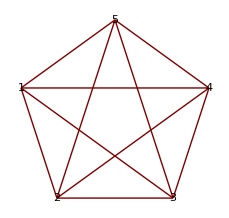
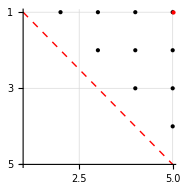

[1] p ={1,2,3,4,5}

{1,2,3,4,5}

```mathematica
G=Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}];
{DGPlotGraph[G],DGPlotAdjacencyMatrix[G,True]}
p=DGBPOrderBrutalForce[G,True]
```

#### Harder Example: The initial ordering is not valid (brutal force)

```mathematica
nodes={1,2,3,4,5,6};
edges={1<->2,1<->3,1<->4,1<->6,2<->3,2<->4,2<->5,2<->6,3<->4,4<->6,4<->5,5<->6};
G=Graph[nodes,edges];
{DGPlotAdjacencyMatrix[G,True],DGPlotGraph[G]}
p=DGBPOrderBrutalForce[G]
```

#### Harder Example: The initial ordering is not valid (smart search)

```mathematica
nodes={1,2,3,4,5,6};
edges={1<->2,1<->3,1<->4,1<->6,2<->3,2<->4,2<->5,2<->6,3<->4,4<->6,4<->5,5<->6};
G=Graph[nodes,edges];
{DGPlotAdjacencyMatrix[G,True],DGPlotGraph[G]}
p=DGBPOrder[G]
```

#### Much Harder Example: The initial ordering is not valid

```mathematica
nodes={1,2,3,4,5,6};
edges={1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,2<->6,3<->4,4<->6,4<->5,5<->6};
G=Graph[nodes,edges];
{DGPlotGraph[G],DGPlotAdjacencyMatrix[G,True]}
p=DGBPOrderBrutalForce[G]
p=DGBPOrder[G]
```

DGIBPSolver

## Source Code

```mathematica
ClearAll[DGIBPSubG,DGIBPSolver];

DGIBPSubG[G_,k_,branch_,nslices_]:=Module[{i,E,W=G,nodes,ei,ej,dij,lij,uij},
(* Delete vertices k+1,...,numberOfAtoms *)
nodes=Table[i,{i,k+1,Length[VertexList[G]]}];
W=VertexDelete[G,nodes];
E=EdgeList[W];
dij=Table[0,{i,Length[E]}];
lij=Table[0,{i,Length[E]}];
uij=Table[0,{i,Length[E]}];
For[i=1,i≤Length[E],i++,
{lij[[i]],uij[[i]]}=DGEdgeDistanceBounds[G,E[[i]]];
dij[[i]]=DGEdgeWeight[G,E[[i]]];
(* set weight affected by branch *)
ei=E[[i]][[1]];
ej=E[[i]][[2]];
If[ei>ej,{ei,ej}={ej,ei}];
If[ej-ei==3,
dij[[i]]=(uij[[i]]-lij[[i]])/nslices;
dij[[i]]=dij[[i]]*branch[[ej]]+lij[[i]]+dij[[i]]/2.0;
];
];
W=Graph[E,EdgeWeight->dij];
For[i=1,i≤Length[E],i++,
PropertyValue[{W,E[[i]]}, "DistanceBounds"] = {lij[[i]],uij[[i]]};
];
Return[W];
];

DGIBPSolver[G_,nslices_,verbose_:False]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G using natural ordering. *)
Module[
(* local variables *)
{i,k,numberOfAtoms,prune,branch,W,S,SW,work,locwork,tol=10^(-5)},
numberOfAtoms=Length[VertexList[G]];
(* init IBPTree *)
branch=Table[0,{i,numberOfAtoms}];branch[[1;;3]]=nslices-1;
work=Table[0,{i,numberOfAtoms}];work[[1;;3]]=1;
(* solutions and branches *)
S=<|"Points"->{},"Branches"->{}|>;
k=4;
While[k>3,
W=DGIBPSubG[G,k,branch,nslices];
{SW,locwork}=DGBPSolver[W,DGNaturalOrder[W],k≠numberOfAtoms];
For[i=4,i≤k,i++,work[[i]]+=locwork[[i]]];
prune=Length[SW["Points"]]==0; (* unfeasible subgraph *)
(*Print["[ibp] k=",k,"  branch=",branch, "   work=",work," prune=",prune];*)
(* solution found *)
If[Not[prune]&&k==numberOfAtoms ,
S["Points"]=Join[S["Points"],SW["Points"]];
AppendTo[S["Branches"],branch]];
(* update tree node *)
prune=prune||k==Length[branch];
If[prune&&branch[[k]]==nslices-1,
While[k>3&&branch[[k]]==nslices-1,k--];
];
If[prune&&branch[[k]]<nslices-1,
branch[[k]]++;
For[i=k+1,i≤Length[branch],i++,branch[[i]]=0];
];
If[Not[prune],k++];
];
If[verbose,
Print["DGIBPSolver"];
Print["Number of solutions: ",Length[S["Points"]]]
];
Return[{S,work}]
];
```

## Examples and Applications

### Check DGIBPSolver

```mathematica
P=DGRandomMDGP[5,0.1,5.0];
branch={1,1,1,1,0};
nslices=2;
W=DGIBPSubG[P["G"],4,branch,nslices];
DGPrintGraph[P["G"]];
DGPrintGraph[W];
```

### Solving a small instance using DGIBP

```mathematica
P=DGRandomMDGP[5,0.1,5.0];
DGPrintGraph[P["G"]]
```

```mathematica
nslices=2; (* testing increasing the the number of slices*)
{S,work}=DGIBPSolver[P["G"],nslices,True];
Print["S=",S]
```

```mathematica
nslices=3; (* increasing the number of slices *)
{S,work}=DGIBPSolver[P["G"],nslices,True];
```

### Illustrating the tree exponential growth

```mathematica
(* Plot IBP Tree (it can be very slow!!!) *)
numberOfAtoms=5;
numberOfSlices=4; (* or 2 at max *)
node=3;
edges={};
count=3;
For[i=1,i≤2*numberOfSlices,i++,
AppendTo[edges,node->(++count)]
];
T=TreeGraph[edges];
For[k=5,k≤numberOfAtoms,k++,
leafs=Select[VertexList[T],VertexDegree[T,#]===1&];
count=Max[VertexList[T]];
For[i=1,i≤Length[leafs],i++,
node=leafs[[i]];
For[j=1,j≤2*numberOfSlices,j++,
AppendTo[edges,node->(++count)]
]
];
T=TreeGraph[edges];
]
Print[T]
Print["Number of Vertex=",Length[VertexList[T]]]
```

```mathematica
(* Number of nodes on IBP tree *)
NumberOfIBPVertex[numberOfAtoms_,numberOfSlices_]:=Module[{},((2*numberOfSlices)^(numberOfAtoms-2)-1)/((2*numberOfSlices)-1)];
NumberOfIBPVertex[9,4]
```

```mathematica
xy=Table[{i,NumberOfIBPVertex[9,i]},{i,10}];
ListLogPlot[xy,Joined->True,PlotLabel->"Number of Vertex on IBP Tree"]
```

```mathematica
(* Top 1: Sunway TaihuLight at 93 petaflops (10^15 flops) on November 2016 *)
xy=Table[{i,NumberOfIBPVertex[i,4]/(365*24*3600*(93*10^15))},{i,40}];
ListLogPlot[xy,Joined->True,PlotLabel->"Time to compute IBP tree on 93 petaflops",AxesLabel->{"Number of Atoms","Years"}]
```

## 5) Applets

Applet: Continuos Problem

## Moving circles

```mathematica
ClearAll[circle]
circle[a_,b_,dax_,dbx_,color_]:= Module[{dab,dac,dcx,c,n,u,y,z,α,θ,R,resolution=30},
dab=EuclideanDistance[a,b];
θ=ArcCos[(dab^2+dax^2-dbx^2)/(2*dax*dab)];
dac=Cos[θ]*dax;
dcx=Sin[θ]*dax;
n=Normalize[b-a];
c=dac*n+a;
y=dcx*n+c;
If[Abs[n[[1]]]>0,
u=Normalize[{n[[2]],-n[[1]],0}],
u={1,0,0}
];
R=RotationTransform[90Degree,u,c];
y=R[y];
α=Array[#&,resolution,{0,2*Pi}];
z=Table[RotationTransform[α[[i]],n,c][y],{i,resolution}];
Return[Graphics3D[{color,Thick,Line[z]}]]
];

(* covalent bond lenghts *)
d=Table[1.526,{i,7}];
(* plane angles *)
θ=Table[1.91,{i,7}];
(* solution *)
x=DGSetXByHomogeneousCoords[d,θ,{0,0,0,-30Degree,-30Degree,-45Degree,60Degree}];
(* distance matrix *)
A=DistanceMatrix[x];
r[i_,j_]:=A[[i]][[j]];

DynamicModule[{},
Manipulate[
x=DGSetXByHomogeneousCoords[d,θ,{0,0,0,Subscript[ω, 4],Subscript[ω, 5],Subscript[ω, 6],Subscript[ω, 7]}];
(* backbone structure *)
Show[
{
Graphics3D[{
{Gray,Tube[x]},
{PointSize[.02],Red,Point[x[[1;;3]]]},
{PointSize[.02],Purple,Point[x[[4]]]},
{PointSize[.02],Black,Point[x[[5]]]},
{PointSize[.02],Blue,Point[x[[6]]]},
{PointSize[.02],Green,Point[x[[7]]]}
}],
circle[x[[2]],x[[3]],r[2,4],r[3,4],Purple],
circle[x[[3]],x[[4]],r[3,5],r[4,5],Black],
circle[x[[4]],x[[5]],r[4,6],r[5,6],Blue],
circle[x[[5]],x[[6]],r[5,7],r[6,7],Green]
},
PlotRange->{{-5,5},{-5,5},{-5,5}},
RotationAction->"Clip",
AxesLabel->{"x","y","z"},
BoxStyle->Directive[Dashed],
ImageSize->Medium,
Boxed->True,
Axes->True
]
,
Style["Torsion Angles",Bold,Medium],
{{Subscript[ω, 4],0,"ω_4"},-Pi,Pi},
{{Subscript[ω, 5],0,"ω_5"},-Pi,Pi},
{{Subscript[ω, 6],0,"ω_6"},-Pi,Pi},
{{Subscript[ω, 7],0,"ω_7"},-Pi,Pi},
ControlPlacement->Left]
]
```

## Moving circles and sphere

```mathematica
ClearAll[circle,sphere]
circle[a_,b_,dax_,dbx_,color_,dashed_:False]:= Module[{dab,dac,dcx,c,n,u,y,z,α,θ,R,resolution=30},
dab=EuclideanDistance[a,b];
θ=ArcCos[(dab^2+dax^2-dbx^2)/(2*dax*dab)];
dac=Cos[θ]*dax;
dcx=Sin[θ]*dax;
n=Normalize[b-a];
c=dac*n+a;
y=dcx*n+c;
If[Abs[n[[1]]]>0,
u=Normalize[{n[[2]],-n[[1]],0}],
u={1,0,0}
];
R=RotationTransform[90Degree,u,c];
y=R[y];
α=Array[#&,resolution,{0,2*Pi}];
z=Table[RotationTransform[α[[i]],n,c][y],{i,resolution}];
If[dashed,
Return[Graphics3D[{color,Dashed,Thick,Line[z]}]],
Return[Graphics3D[{color,Thick,Line[z]}]]
]
];

sphere[c_,r_]:=ParametricPlot3D[c+r*{Cos[θ]*Sin[ϕ],Sin[θ]*Sin[ϕ],Cos[ϕ]},
{θ,0,2*Pi},
{ϕ,0,Pi},
Mesh->None,
PlotStyle->Red];

(* covalent bond lenghts *)
d=Table[1.526,{i,6}];
(* plane angles *)
θ=Table[1.91,{i,6}];
(* solution *)
x=DGSetXByHomogeneousCoords[d,θ,{0,0,0,-30Degree,-45Degree,60Degree}];
(* distance matrix *)
A=DistanceMatrix[x];
r[i_,j_]:=A[[i]][[j]];

DynamicModule[{x,p},
Manipulate[
x=DGSetXByHomogeneousCoords[d,θ,{0,0,0,Subscript[ω, 4],Subscript[ω, 5],Subscript[ω, 6]}];
p={};
(* backbone structure *)
AppendTo[p,Graphics3D[{{Gray,Tube[x]},{PointSize[.02],Blue,Point[x]}}]];
If[Subscript[s, 5],AppendTo[p,sphere[x[[5]],r[5,6]]]];
If[Subscript[c, 45],AppendTo[p,circle[x[[4]],x[[5]],r[4,6],r[5,6],Blue]]];
If[Subscript[c, 35],AppendTo[p,circle[x[[3]],x[[5]],(2-Subscript[ϵ, 36])*r[3,6],r[5,6],Black]]];
If[And[Subscript[c, 35],Subscript[ϵ, 36]<1],AppendTo[p,circle[x[[3]],x[[5]],Subscript[ϵ, 36]*r[3,6],r[5,6],Black,True]]];
If[Subscript[c, 15],AppendTo[p,circle[x[[1]],x[[5]],(2-Subscript[ϵ, 16])*r[1,6],r[5,6],Yellow]]];
If[And[Subscript[c, 15],Subscript[ϵ, 16]<1],AppendTo[p,circle[x[[1]],x[[5]],Subscript[ϵ, 16]*r[1,6],r[5,6],Yellow,True]]];
Show[
p,
PlotRange->{{-5,5},{-5,5},{-5,5}},
RotationAction->"Clip",
AxesLabel->{"x","y","z"},
BoxStyle->Directive[Dashed],
ImageSize->Medium,
Boxed->False,
Axes->False
]
,
Style["Torsion Angles",Bold,Medium],
{{Subscript[ω, 4],-30Degree},-Pi,Pi},
{{Subscript[ω, 5],-45Degree},-Pi,Pi},
{{Subscript[ω, 6],60Degree},-Pi,Pi},
Delimiter,
Style["Display sphere and circles",Bold,Medium],
{{Subscript[s, 5],False," Sphere[5,6]"},{True,False}},
{{Subscript[c, 45],False," Circle[4,5,6]"},{True,False}},
{{Subscript[c, 35],False," Circle[3,5,6]"},{True,False}},
{{Subscript[c, 15],False," Circle[1,5,6]"},{True,False}},
Delimiter,
Style["Precision",Bold,Medium],
{{Subscript[ϵ, 36],1},0,1},
{{Subscript[ϵ, 16],1},0,1},
ControlPlacement->Left]
]
```

## Solving using rotations

```mathematica
ClearAll[DGByHandGetX,DGByHandErrorMatrix];
DGByHandGetX[θ_]:=Module[{n,d=1.526,ϕ=1.91,a,b,c,i,p,u,v,x},
n=Length[θ];
x=Table[0,{i,n},{j,3}];
x[[{1,2,3}]]={{0,0,0},{-d,0,0},{-d+d*Cos[ϕ],d*Sin[ϕ] ,0}};
For[i=4,i≤n,i++,
(* dihedral rotation axis *)
{a,b,c}={x[[i-3]],x[[i-2]],x[[i-1]]};
u=Normalize[b-c];
p= c+d* u; 
(* normal to the plane abc *)
v=Cross[b-c,a-c];
(* plane rotation *)
p=RotationTransform[ϕ,v,c][p];
(* dihedral rotation *)
p=RotationTransform[θ[[i]],u,c][p];
(* set i-th coordinate *)
x[[i]]=p
];
Return[x]
];

DGByHandErrorMatrix[G_,x_]:=Module[{i,j,k,edges,M,dij},
M=Table[0,{i,Length[x]},{j,Length[x]}];
edges=EdgeList[G];
For[k=1,k≤Length[edges],k++,
i=edges[[k]][[1]];
j=edges[[k]][[2]];
dij=DGEdgeWeight[G,i<->j];
M[[i]][[j]]=Abs[(Norm[x[[i]]-x[[j]]]-dij)/dij];
M[[j]][[i]]=M[[i]][[j]];
];
Return[M]
];

ω=RandomReal[{-Pi,Pi},9]
x=DGByHandGetX[ω];
G=DGProblem[x]["G"];
DynamicModule[{},
Manipulate[{
Graphics3D[{
{Red,Tube[DGByHandGetX[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]]},
{PointSize[Large],Blue,Point[DGByHandGetX[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]]}},
PlotRange->{xrange,yrange,zrange},
RotationAction->"Clip",
Axes->True,
AxesLabel->{"x","y","z"},
PlotLabel->{"Mean(error):",NumberForm[Max[DGByHandErrorMatrix[G,DGByHandGetX[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]]],{3,2}]},
BoxStyle->Directive[Dashed],
ImageSize->Medium],
MatrixPlot[DGByHandErrorMatrix[G,DGByHandGetX[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]],ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False]},
(* Torsion angles *)
Style["Torsion Angles",Bold,Medium],
{{ω4,0},-Pi,Pi},
{{ω5,0},-Pi,Pi},
{{ω6,0},-Pi,Pi},
{{ω7,0},-Pi,Pi},
{{ω8,0},-Pi,Pi},
{{ω9,0},-Pi,Pi},
(* Bounding boxes *)
Style["Bounding Limits",Bold,Medium],
{{xrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
{{yrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
{{zrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
OpenerView[
{Style["Solution",Bold, Medium],
Column[
{Row[{"ω4  ",Slider[ω[[4]],{-Pi,Pi},Enabled->False]}],
Row[{"ω5  ",Slider[ω[[5]],{-Pi,Pi},Enabled->False]}],
Row[{"ω6  ",Slider[ω[[6]],{-Pi,Pi},Enabled->False]}],
Row[{"ω7  ",Slider[ω[[7]],{-Pi,Pi},Enabled->False]}],
Row[{"ω8  ",Slider[ω[[8]],{-Pi,Pi},Enabled->False]}],
Row[{"ω9  ",Slider[ω[[9]],{-Pi,Pi},Enabled->False]}]}]}],
ControlPlacement->Left]
]
```

Applet: Discrete Problem (BP)

## The complexity explosion

Com n átomos, teremos 2^(n-3) vértices no nível mais de baixo da árvore binária (folhas). Supondo que cada uma das configurações associadas às folhas da árvore binária possa ser testada em uma única operação em ponto flutuante, quanto tempo levaria para testar/explorar todas as configurações?

Esta resposta obviamente depende de quantas operações em ponto flutante um computador pode fazer por segundo. Tomando como referência o computador TaihuLight mais rápido em junho de 2017 (Top500) que pode fazer 93×10^15 operações por segundo, uma instância com 2^(n-3) átomos poderia ser resolvida em 

TempoTotal(n) =   2^(n - 3)/(93×10^15)

```mathematica
xy=Table[{n,(2^(n-3))/(365*24*3600*93*10^15)},{n,100}]; (* checar segundos, horas, dias e anos *)
ListLogPlot[xy,Joined->True,PlotLabel->"Time to evaluate all nodes on BP Tree",AxesLabel->{"Number of Atoms","Time"}]
```

## Applet

```mathematica
ClearAll[DGByHandTreeFromBranches]
DGByHandTreeFromBranches[G_,branch_,branches_,checkBP_]:=Module[
{T,X,k,i,n,b,x,y,z,dx,dy,dz,edges={},v={},styVertex,styEdges={},m,color,valid,nid},
nid=DGBPNaturalOrder[G];
n=Length[VertexList[G]]-3;
(* creating edges *)
For[k=1,k≤2^n-1,k++,
AppendTo[edges,k<->2k];
AppendTo[edges,k<->2k+1];
];
(* highlighting current branch *)
For[k=0,k≤n,k++,
AppendTo[v,FromDigits[Join[{1},branch[[1;;k]]],2]];
If[k>0,
AppendTo[styEdges,v[[k]]<->v[[k+1]]->{Blue,Thickness[0.01]}]
];
];
(* coloring visited nodes (branches) *)
styVertex={LightGray};
If[Length[branches]>0,
For[k=1,k≤Length[branches],k++,
X=DGBPXinit[G,nid[[1;;3]]];
b=branches[[k]];
If[checkBP,
(* checking partial solutions (checkBP=True) *)
For[i=1,i≤n,i++,
X[[i+3]]=DGBPGetX[G,X,b[[i]],nid,i+3];
If[DGRelativeResidue[G,X,nid,i+3]<0.001,
color=Green,(* if true *)
color=Red (* if false *)
];
v=FromDigits[Join[{1},b[[1;;i]]],2];
AppendTo[styVertex,v->color]
],
(* checking only final solution *)
valid=True;
For[i=1,i≤n,i++,
X[[i+3]]=DGBPGetX[G,X,b[[i]],nid,i+3];
If[DGRelativeResidue[G,X,nid,i+3]>0.001,
valid=False
];
If[valid,color=Green,color=Red];
v=FromDigits[Join[{1},b],2];
AppendTo[styVertex,v->color]
],
];
];
];
T=TreeGraph[
edges,
VertexStyle->styVertex,
EdgeStyle->styEdges,
GraphLayout->{"LayeredEmbedding",LayerSizeFunction->(8&)}
];
Return[T];
];
(* set minimal edge set *)
P=DGRandomMDGP[9,0.0,0.0]; (* it must be a graph with 9 nodes *)
edges=EdgeList[P["G"]];
(* add extra constraints *)
edges=Union[edges,{2<->7},{1<->5}];
(* init graph *)
G=DGProblem[DGRandom3DBackbone[9]["Points"],edges]["G"];
(* set order *)
nodes=DGBPNaturalOrder[P["G"]];
DynamicModule[{branches={},b={},s={},node,X=DGBPXinit[G,nodes[[1;;3]]]},
Manipulate[
Row[{DGByHandTreeFromBranches[G,{ω4,ω5,ω6,ω7,ω8,ω9},branches,BP],
Column[
{DGPlotAdjacencyMatrix[G,Sym],
Graphics3D[{
{Red,Tube[X]},
{PointSize[Large],Blue,Point[X]}}],
MatrixForm[s,TableHeadings->{None,{"ω4","ω5","ω6","ω7","ω8","ω9"}}]}]}],
(* Branches *)
Style["Branches",Bold,Medium],
{ω4,{0,1},ControlType->SetterBar},
{ω5,{0,1},ControlType->SetterBar},
{ω6,{0,1},ControlType->SetterBar},
{ω7,{0,1},ControlType->SetterBar},
{ω8,{0,1},ControlType->SetterBar},
{ω9,{0,1},ControlType->SetterBar},
Button["Try",
{b={ω4,ω5,ω6,ω7,ω8,ω9},
For[node=1,node≤Length[b],node++,
X[[node+3]]=DGBPGetX[G,X,b[[node]],nodes,node+3];
],
AppendTo[branches,{ω4,ω5,ω6,ω7,ω8,ω9}]},
Background->LightBlue],
Delimiter,
Style["Options",Bold, Medium],
{BP,{False,True},ControlType->Checkbox},
{Sym,{False,True},ControlType->Checkbox},
Delimiter,
(* show solutions *)
Style["Solutions",Bold,Medium],
Button["Show",
{s=DGBPSolver[G,nodes][[1]]["Branches"],
s=Table[s[[i]][[j]],{i,Length[s]},{j,4,9}],
branches=Union[branches,s]},
Background->LightRed
],
Button["Reset",
{G=DGProblem[DGRandom3DBackbone[9]["Points"],edges]["G"],branches={},b={},s={}},
Background->LightRed]
],
ControlPlacement->Left
]
```

## 6) Solving IMDGP using Rotations

### DGRotAngleInterval

```mathematica
ClearAll[DGGetRotAngleInterval]
DGGetRotAngleInterval[dab_,dac_,dbc_,dax_,dbx_,lcx_,ucx_]:=
Module[{a,b,c,r,q,ω,θ,χ,ρ,lcxMin,ucxMax,verbose=False},
(* creates the base triangle *)
a={0,0,0};
b={dab,0,0};
θ=ArcCos[(dab^2+dac^2-dbc^2)/(2*dac*dab)];
c=dac{Cos[θ],Sin[θ],0};
If[verbose,Print["{a,b,c}=",{a,b,c}]];
(* intersection of the circunference and the positive quadrant of XY-Plane *)
θ=ArcCos[(dab^2+dax^2-dbx^2)/(2*dab*dax)];
If[verbose,Print["θ=",θ]];
q=dax{Cos[θ],Sin[θ],0}; (* intersection *)
r=q[[2]];(* circle radius *)
If[verbose,Print["{q,r}=",{q,r}]];
If[verbose,Print["{daq,dbq}=",{Norm[a-q],Norm[b-q]}]];
(* circunference parametrization *)
χ[θ_]:={q[[1]],r*Cos[θ],r*Sin[θ]};
If[verbose,Print["{lcx,ucx}=",{lcx,ucx}]];
lcxMin=Max[lcx,Norm[c-χ[0.01]]];
ucxMax=Min[ucx,Norm[c-χ[π-0.01]]];
If[verbose,Print["{lcxMin,ucxMax}=",{lcxMin,ucxMax}]];
(* calculates rotation angle given a distance to point c *)
ρ[δ_]:=ArcCos[((q[[1]]-c[[1]])^2+r^2+c[[2]]^2-δ^2)/(2r*c[[2]])];
ω={ρ[lcxMin],ρ[ucxMax]};
Return[ω]
]
```

#### Example

```mathematica
(* calculating rotation angle bounds *)
a={0,0,0};b={2,0,0};c={2,1,0};x={1,0,1};
ϵ=0.1;
dab=Norm[a-b];dac=Norm[a-c];dbc=Norm[b-c];
dax=Norm[a-x];dbx=Norm[b-x];dcx=Norm[c-x];
ucx=(1+ϵ)*dcx;
lcx=(1-ϵ)*dcx;
ω=DGGetRotAngleInterval[dab,dac,dbc,dax,dbx,lcx,ucx]
```

### DGGetAllRotAngleInterval

```mathematica
ClearAll[DGGetAllRotAngleInterval]
DGGetAllRotAngleInterval[G_]:=Module[{natoms,ω,dab,dac,dbc,dax,dbx,lcx,ucx,i,j},
natoms=Length[VertexList[G]];
ω=Table[0,{i,natoms},{j,2}];
For[i=4,i≤natoms,i++,
dab=DGEdgeWeight[G,(i-1)<->(i-2)];
dac=DGEdgeWeight[G,(i-1)<->(i-3)];
dbc=DGEdgeWeight[G,(i-2)<->(i-3)];
dax=DGEdgeWeight[G,(i-1)<->i];
dbx=DGEdgeWeight[G,(i-2)<->i];
{lcx,ucx}=DGEdgeDistanceBounds[G,(i-3)<->i];
ω[[i]]=DGGetRotAngleInterval[dab,dac,dbc,dax,dbx,lcx,ucx];
];
Return[ω];
];
```

#### Example

```mathematica
(* Creates a random problem *)
P=DGRandomMDGP[5,0.1,5,0];
G=P["G"];
DGPlotAdjacencyMatrix[G]
ω=DGGetAllRotAngleInterval[G]
```

### DGSolverRot

```mathematica
ClearAll[DGSolverRot]
DGSolverRot[G_,β_,nodes_,nsample_]:=
Module[{natoms,ω,i,j,θ,ϕ,ρ,ϵ,a,b,c,n,p,q,x,dab,dac,dbc,dax,dbx,dcx,X,isSolution},
natoms=Length[VertexList[G]];
ω=DGGetAllRotAngleInterval[G];
(* set the first triangle *)
dab=DGEdgeWeight[G,1<->2];
dac=DGEdgeWeight[G,1<->3];
dbc=DGEdgeWeight[G,2<->3];
X={};isSolution={};
For[j=1,j≤nsample,j++,
x=Table[{0,0,0},{i,natoms}];
x[[2]]={dab,0,0};
θ=ArcCos[(dab^2+dac^2-dbc^2)/(2*dac*dab)];
x[[3]]=dac{Cos[θ],Sin[θ],0};
(*Print["x[1]=",x[[1]]];*)
(*Print["x[2]=",x[[2]]];*)
(*Print["x[3]=",x[[3]]];*)
(* select random rotation angles *)
For[i=4,i≤natoms,i++,
(* get distances *)
dab=DGEdgeWeight[G,(i-1)<->(i-2)];
dac=DGEdgeWeight[G,(i-1)<->(i-3)];
dbc=DGEdgeWeight[G,(i-2)<->(i-3)];
dax=DGEdgeWeight[G,(i-1)<->i];
dbx=DGEdgeWeight[G,(i-2)<->i];
(*Print["dax=",dax];*)
a=x[[i-1]];b=x[[i-2]];c=x[[i-3]];
(* circunference center *)
θ=ArcCos[(dab^2+dax^2-dbx^2)/(2dab*dax)];
p=a+Normalize[b-a]*Cos[θ]*dax;
(*Print["{θ,p}=",{θ,p}];*)
(* intersection of circunference and the triangle abc *)
n=Cross[b-a,c-a];
q=p+Normalize[Cross[n,b-a]]*Sin[θ]*dax;
(*Print["{n,q}=",{n,q}];*)
(*Print["{daq,dbq}=",{Norm[a-q],Norm[b-q]}];*)
(* random rotation angle *)
ϕ=RandomReal[ω[[i]]];
ρ=RotationTransform[(-1)^β[[i]]*ϕ,b-a,a];
x[[i]]=ρ[q];
];
AppendTo[X,x];
];
Return[X];
]
```

#### Example

```mathematica
(* Creates a random problem *)
natoms=7;
P=DGRandomMDGP[natoms,0.1,5,0];
G=P["G"];
DGPlotAdjacencyMatrix[G]
nodes=Table[i,{i,natoms}];
β=RandomChoice[{0,1},natoms];
```

```mathematica
x=DGSolverRot[G,β,nodes,5];
DGPlot3DBackbone[x,0.2,0.08]
For[i=1,i≤Length[x],i++,
Print["Maximum Relative Residue of x[",i,"]: ",Max[DGRelativeResidue[G,x[[i]]]]]
];
```